## General dataframe helpers

Every type of dataframe has an associated header list, giving the variables names for the columns.

Callinng DefineDataframeHelpers defines helper functionst that allow filtering and querying by variable name, instead of column index.

```mathematica
(* Defines dataframe helpers based on a header *)
DefineDataframeHelpers[header_]:=Module[{ColNum},
ColNum[var_String]:=Position[header,var]⟦1,1⟧;

GroupByVar[var_String,data_]:=With[{colNum=ColNum[var]},SplitBy[data,#⟦colNum⟧&]];
WhereVarEq[var_String,varValue_,data_]:=With[{col=ColNum[var]},Select[data,(#⟦col⟧==varValue)&]];
WhereVarsEq[var1_String,var1Value_,var2_String,var2Value_,data_]:=
With[{col1=ColNum[var1],col2=ColNum[var2]},Select[data,And[(#⟦col1⟧==var1Value),#⟦col2⟧==var2Value]&]];
JustVar[var1_String,data_List]:=With[{col=ColNum[var1]},Part[data,All,col]];
JustVars[var1_String,var2_String,data_]:=
With[{col1=ColNum[var1],col2=ColNum[var2]},Part[data,All,{col1,col2}]];
DataframeForm[table_]:=TableForm[table,
TableHeadings->{None,header},TableAlignments->"."];];
```

This reads a dataframe from a file, where the file has headers on the first line and numerical data on following lines

```mathematica
(* Reads a dataframe, defines helpers based on its header *)
ReadDataframe[file_]:=Module[{stream,header,results},
stream=OpenRead[file];
header=ReadList[StringToStream[ToString[ReadList[stream,String,1]⟦1⟧]],Word];
DefineDataframeHelpers[header];
results=ReadList[stream,Number,RecordLists->True];
results]
```

## Wrapper for Clusters

```mathematica
Directory[]
```

/Users/alexis

```mathematica
SetDirectory["/Users/alexis/workspace/clustersearch/cpp/build"]
```

/Users/alexis/workspace/clustersearch/cpp/build

This function wrap the program “clusters”, which outputs a dataframe when called with both --verbose=1 and --header

```mathematica
Clusters::usage ="Clusters[alpha,length,colors,power, samples] Populates a dataframe with data from clusters, using randomstart, seed=1";
Clusters[alpha_,length_,colors_,power_,samples_:10]:=
(* Returns data of cluster_size, perimeter_size, colors, exits_size, robustness *)
Module[{seed=1,randomstart=True,mode="data",args,command},
args="";
args = StringJoin[args," ", "--alpha=",     ToString[alpha]];
args = StringJoin[args," ", "--length=",   ToString[length]];
args = StringJoin[args," ", "--colors=",   ToString[colors]];
args = StringJoin[args," ", "--power=",     ToString[power]];
If[randomstart,args = StringJoin[args," ", "--randomstart"]];
args = StringJoin[args," ", "--samples=", ToString[samples]];
args = StringJoin[args," ", "--seed=",       ToString[seed]];
args = StringJoin[args," ", "--mode=",       ToString[mode]];
args = StringJoin[args," ", "--header"];
args = StringJoin[args," ", "--verbose=1"];
command=StringJoin["!./clusters",args];
ReadDataframe[command]]
```

## Displaying Results

```mathematica
(* Draws and E vs r DensityHistogram,
   holding m and k constant
   sourcing from a Clusters dataframe *)
HeatmapEvsr[m_,k_,dataframe_]:=
StatusArea[
DensityHistogram[
 dataframe // (WhereVarsEq["m",m,"k",k,#]&)// JustVars["E","r",#]&,
PlotRange->{{0,m},{0,1}} ,
FrameLabel->{"E","r"},
ColorFunction->Function[{height},Opacity[height]],
ChartBaseStyle->Black],
StringJoin["m=",ToString[m],", k=",ToString[k]]];
```

```mathematica
HistogramOfS[m_,k_,dataframe_]:=
StatusArea[
Histogram[ dataframe // (WhereVarsEq["m",m,"k",k,#]&) // JustVar["s",#]&],
StringJoin["m=",ToString[m],", k=",ToString[k]]];
```

```mathematica
HistogramOfE[m_,k_,dataframe_]:=
StatusArea[
Histogram[ dataframe //(WhereVarsEq["m",m,"k",k,#]&) // JustVar["E",#]&],
StringJoin["m=",ToString[m],", k=",ToString[k]]];
```

```mathematica
With[{data=data},
Histogram3D[( data //JustVars["E","r",#]&),
AxesLabel->{"E","r"}]]
```

-Graphics3D-

## Examples of analysis

### Generating data and viewing it as a table

For example, we can search one cluster given binary length-10 strings with 4 colors:.

```mathematica
Clear[data];
data = Clusters[2,10,4,0]
```

{{2,10,4,0,261,705,3,1862,0.28659},{2,10,4,0,252,716,3,1826,0.275397},{2,10,4,0,236,724,3,1746,0.260169},{2,10,4,0,212,690,3,1612,0.239623},{2,10,4,0,194,699,3,1502,0.225773},{2,10,4,0,231,712,3,1680,0.272727},{2,10,4,0,220,705,3,1634,0.257273},{2,10,4,0,199,656,3,1482,0.255276},{2,10,4,0,248,704,3,1764,0.28871},{2,10,4,0,231,720,3,1712,0.258874}}

```mathematica
data // DataframeForm
```

a | l | m | k | s | t | E | u | r
2 | 10 | 4 | 0 | 261 | 705 | 3 | 1862 | 0.28659
2 | 10 | 4 | 0 | 252 | 716 | 3 | 1826 | 0.275397
2 | 10 | 4 | 0 | 236 | 724 | 3 | 1746 | 0.260169
2 | 10 | 4 | 0 | 212 | 690 | 3 | 1612 | 0.239623
2 | 10 | 4 | 0 | 194 | 699 | 3 | 1502 | 0.225773
2 | 10 | 4 | 0 | 231 | 712 | 3 | 1680 | 0.272727
2 | 10 | 4 | 0 | 220 | 705 | 3 | 1634 | 0.257273
2 | 10 | 4 | 0 | 199 | 656 | 3 | 1482 | 0.255276
2 | 10 | 4 | 0 | 248 | 704 | 3 | 1764 | 0.28871
2 | 10 | 4 | 0 | 231 | 720 | 3 | 1712 | 0.258874

```mathematica
data// Mean
```

{2,10,4,0,1142/5,7031/10,3,1682,0.262041}

```mathematica
Mean /@ Transpose[data]
```

{2,10,4,0,1142/5,7031/10,3,1682,0.262041}

```mathematica
List[Mean[data]] // DataframeForm
```

a | l | m | k | s | t | E | u | r
2 | 10 | 4 | 0 | 1142/5 | 7031/10 | 3 | 1682 | 0.262041

### Generating data ranging over 1 input variable (colors)

Generate data frame where we

hold constant
   alpha =2
   length=10 
   samples = 15
   gray=0

let 
  colors range from 2 to 5,
 
We use Table to generate dataframe for each value of colors, then flatten once to reduce it to one dataframe

```mathematica
Clear[data];
data = With[{alpha=2,length=8,samples=4,power=0},
Table[Clusters[alpha,length,colors,power,samples],
{colors,2,4}]] // Flatten[#,1]& ;
```

Display it as a table with headings

```mathematica
data // DataframeForm
```

a | l | m | k | s | t | E | u | r
2 | 8 | 2 | 0 | 135 | 120 | 1 | 502 | 0.535185
2 | 8 | 2 | 0 | 131 | 124 | 1 | 514 | 0.509542
2 | 8 | 2 | 0 | 114 | 140 | 1 | 508 | 0.442982
2 | 8 | 2 | 0 | 125 | 130 | 1 | 544 | 0.456
2 | 8 | 3 | 0 | 88 | 162 | 2 | 470 | 0.332386
2 | 8 | 3 | 0 | 91 | 154 | 2 | 446 | 0.387363
2 | 8 | 3 | 0 | 88 | 164 | 2 | 432 | 0.386364
2 | 8 | 3 | 0 | 80 | 168 | 2 | 426 | 0.334375
2 | 8 | 4 | 0 | 21 | 88 | 3 | 124 | 0.261905
2 | 8 | 4 | 0 | 1 | 8 | 3 | 8 | 0
2 | 8 | 4 | 0 | 52 | 151 | 3 | 298 | 0.283654
2 | 8 | 4 | 0 | 49 | 154 | 3 | 286 | 0.270408

### Averaging data to study means

Group by m (colors):

```mathematica
DataframeForm /@ GroupByVar["m",data]
```

{a | l | m | k | s | t | E | u | r
2 | 8 | 2 | 0 | 135 | 120 | 1 | 502 | 0.535185
2 | 8 | 2 | 0 | 131 | 124 | 1 | 514 | 0.509542
2 | 8 | 2 | 0 | 114 | 140 | 1 | 508 | 0.442982
2 | 8 | 2 | 0 | 125 | 130 | 1 | 544 | 0.456,a | l | m | k | s | t | E | u | r
2 | 8 | 3 | 0 | 88 | 162 | 2 | 470 | 0.332386
2 | 8 | 3 | 0 | 91 | 154 | 2 | 446 | 0.387363
2 | 8 | 3 | 0 | 88 | 164 | 2 | 432 | 0.386364
2 | 8 | 3 | 0 | 80 | 168 | 2 | 426 | 0.334375,a | l | m | k | s | t | E | u | r
2 | 8 | 4 | 0 | 21 | 88 | 3 | 124 | 0.261905
2 | 8 | 4 | 0 | 1 | 8 | 3 | 8 | 0
2 | 8 | 4 | 0 | 52 | 151 | 3 | 298 | 0.283654
2 | 8 | 4 | 0 | 49 | 154 | 3 | 286 | 0.270408}

Group by m (colors) and average each group to create a new dataframe of means, not data.

```mathematica
(Mean /@ GroupByVar["m",data]) // DataframeForm
```

a | l | m | k | s | t | E | u | r
2 | 8 | 2 | 0 | 505/4 | 257/2 | 1 | 517 | 0.485927
2 | 8 | 3 | 0 | 347/4 | 162 | 2 | 887/2 | 0.360122
2 | 8 | 4 | 0 | 123/4 | 401/4 | 3 | 179 | 0.203992

Extract just m vs <r>, and plot it

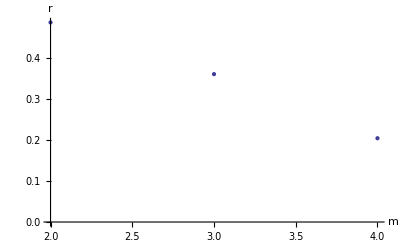

```mathematica
ListPlot[JustVars["m","r", (Mean /@ GroupByVar["E",data])],AxesLabel->{"m","r"}]
```

### Graphing distributional data

Generate large number of samples per value of mm

```mathematica
Clear[data];
data = With[{alpha=2,length=8,samples=1000,power=0},
Table[Clusters[alpha,length,colors,power,samples],
{colors,2,4}]] // Flatten[#,1]& ;
```

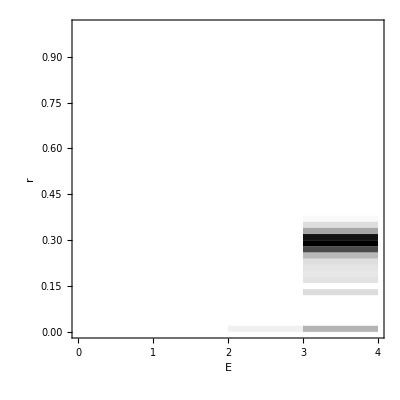

```mathematica
HeatmapEvsr[4,0,data]
```

```mathematica
Histogram3D[JustVars["E","r",WhereVarEq["m",4,data]],AxesLabel->{"E","r"}]
```

-Graphics3D-

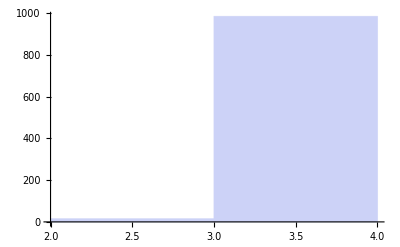

```mathematica
HistogramOfE[4,0,data]
```

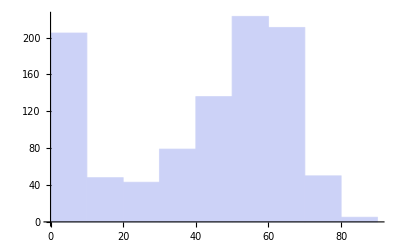

```mathematica
HistogramOfS[4,0,data]
```

In the grid below, k is increasing from left to right, and m is increasing from top to bottom.

Within each grid cell, E is increasing from left to right, and r is increasing from bottom to top

```mathematica
With[{data=data},
GraphicsGrid[Table[
With[{m=m,k=k},
DensityHistogram[
 Map[List[(#⟦1⟧/(m-1)),(#⟦2⟧)] &, 
JustVars["E","r",data // WhereVarEq["m",m,#]& // WhereVarEq["k",k,#]&]],
PlotRange->{{0,1.1},{0,1}} ,
AxesLabel->{"E","r"},
ColorFunction->Function[{height},Opacity[height]],
ChartBaseStyle->Black,
PerformanceGoal->"Speed"]],
{m,8,40,8},{k,0,4,0.5}]]]
```

-Graphics-

### Miscellaneous

```mathematica
rawdata = Clusters[2,30,40,0,25000,"data"];
```

```mathematica
N /@ Mean /@ Transpose[rawdata]
```

{3.48216,96.7954,28.496,99.4558,0.0248988}

```mathematica
SelectEandr[clustersdata_]:=clustersdata // JustVars["E","r",#]&
```

```mathematica
PlotEandr[clustersdata_]:=ListPlot[SelectEandr[clustersdata],AxesLabel->{"E","r"}]
```

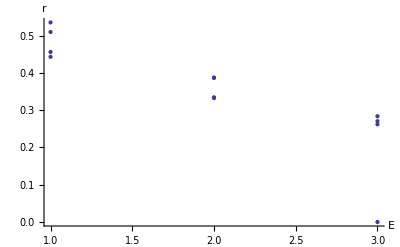

```mathematica
PlotEandr[data]
```

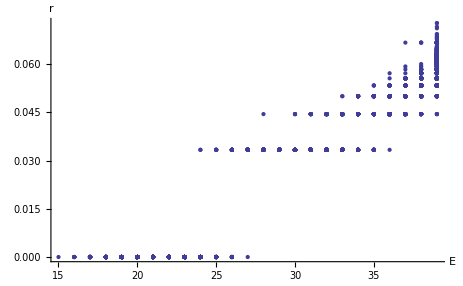

```mathematica
ListPlot[SelectEandr[rawdata],AxesLabel->{"E","r"}]
```

```mathematica
rawdata[30] = Clusters[2,30,30,0,5000,"data"];
rawdata[32] = Clusters[2,30,32,0,5000,"data"];
rawdata[35] = Clusters[2,30,35,0,5000,"data"];
rawdata[40] = Clusters[2,30,40,0,5000,"data"];
rawdata[60] = Clusters[2,30,60,0,5000,"data"];
rawdata[100] = Clusters[2,30,100,0,5000,"data"];
```

```mathematica
AbsoluteTiming[
rawdata12[30] = Clusters[2,12,6,0,5000,"data"];
rawdata12[32] = Clusters[2,12,12,0,5000,"data"];
rawdata12[35] = Clusters[2,12,18,0,5000,"data"];
rawdata12[40] = Clusters[2,12,24,0,5000,"data"];
rawdata12[60] = Clusters[2,12,32,0,5000,"data"];
rawdata12[100] = Clusters[2,12,64,0,5000,"data"];]
```

{141.32454,Null}

```mathematica
Histogram3D[
Map[SelectEandr,{rawdata[30],rawdata[35],rawdata[40],rawdata[60],rawdata[100]}],AxesLabel->{"E","r"}]
```

-Graphics3D-

```mathematica
Histogram3D[
Map[SelectEandr,{rawdata12[30],rawdata12[35],rawdata12[40],rawdata12[60],rawdata12[100]}],AxesLabel->{"E","r"}]
```

-Graphics3D-

```mathematica
dataRangingM = ParallelTable[SelectEandr[Clusters[2,12,m,0,50000,"data"]],{m,10,14}]
```

```mathematica
Histogram3D[dataRangingM,AxesLabel->{"E","r"}]
```

-Graphics3D-

```mathematica
(* Generate Clusters2 dataframe, ranging on m and k  *)
data=With[
{alpha=2,
length=8,
randomstart=True,
samples=2,
mode="data"},
Table[Clusters2[alpha,length,colors,power,randomstart,samples,mode],
{colors,{8,12,14}},
{power, {0,0.1,2,3}}]] // (Flatten[#,2]&)
```

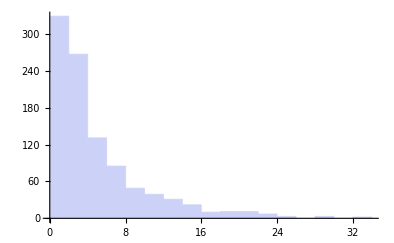

```mathematica
HistogramS[8,0,data]
```

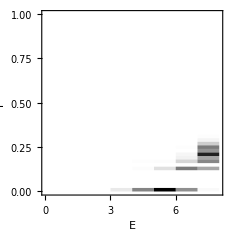

```mathematica
(* single heatmap with m=8,k=0 *)
With[{m=8,k=0,dataframe=data},
HeatmapEvsr[m,k,dataframe]]
```

```mathematica
(* Grid ranging in m and k, of E vs r density histograms,
   drawn from a dataframe produced by Clusters2 *)
With[{dataframe=data},
GraphicsGrid[
HeatmapEvsr[m,k,dataframe],
{m,8,40,8},{k,0,4,0.5}]]
```

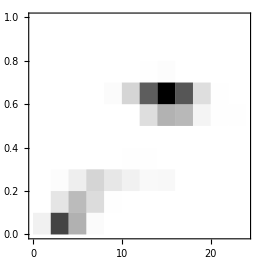

```mathematica
Length[data]
```

410000